## Governing Equations

Conservation of mass

```mathematica
mass conservation = 1/r^2 Dt[ρ u r^2,r]==q;
```

Conservation of momentum

```mathematica
momentum conservation =ρ u Dt[u,r]+Dt[p,r]==-q u -GM/r^2 ρ;
```

Conservation of energy

```mathematica
energy conservation=(1/r^2 Dt[r^2 ρ u(1/2 u^2+(γ p/ρ)/(γ-1)),r]==1/2 q vw^2-GM/r^2 ρ u/.Dt[γ,_]:>0);
```

Mass source term

```mathematica
mass source=DD r^-η;
```

## Reduction to Dimensionless variable

Bondi radius

```mathematica
bondi radius=GM/vw^2;
```

Bondi density

```mathematica
DD*(bondi radius)^-η*(bondi radius/vw);
PowerExpand[%];
bondi density=%;
```

Mass conservation

```mathematica
{mass conservation,momentum conservation,energy conservation};
% /. q-> mass source;
% /. HoldPattern[Dt[z_,r]]->  Dt[z,ξ]/Dt[r,ξ];
% /. p-> bondi density*vw^2*p;
% /. ρ-> bondi density ρ;
% /. u-> vw u;
% /. r-> bondi radius*ξ;
% /. Dt[η,_]:>0;
% /. Dt[DD,_]:>0;
% /. Dt[vw,_]:>0;
% /. Dt[GM,_]:>0;
% /. Dt[γ,_]:>0;
Simplify[%];
Solve[%,{Dt[ρ,ξ],Dt[u,ξ],Dt[p,ξ]}][[1]];
PowerExpand[%];
Simplify[%];
dimles derivs=%;
```

## Integral expressions

Mass conservation

```mathematica
mass source;
%*r^2;
Integrate[%,r];
%-(%/.r->rs);
ρ u r^2==%;
integral mass conservation=%
```

r^2 u ρ==(DD r^(3-η))/(3-η)-(DD rs^(3-η))/(3-η)

Validation

```mathematica
integral mass conservation;
Dt[%,r];
% /. Solve[mass conservation,Dt[ρ,_]][[1]];
% /. q-> mass source;
% /. Dt[DD,_]:>0;
% /. Dt[η,_]:>0;
% /. Dt[rs,_]:>0;
Simplify[%]
```

True

Energy conservation

```mathematica
-(GM u ρ)/r^2;
% /. Solve[integral mass conservation,ρ][[1]];
%*r^2;
Integrate[%,r];
%-(%/.r->rs);
%/integral mass conservation[[2]];
Simplify[%];
1/2 u^2-1/2 vw^2+c^2/(γ-1)==%;
integral energy conservation=%
```

u^2/2-vw^2/2+c^2/(-1+γ)==(GM (r^3 rs^η+r^(1+η) rs^2 (-3+η)-r^η rs^3 (-2+η)))/(r (-r^η rs^3+r^3 rs^η) (-2+η))

Validation

```mathematica
integral energy conservation;
%[[1]]*integral mass conservation[[2]]==%[[2]]*integral mass conservation[[2]];
% /. c-> √(γ p/ρ);
Dt[%,r];
% /. Solve[{mass conservation,
momentum conservation,
energy conservation},{Dt[p,r],Dt[ρ,r],Dt[u,r]}][[1]];
% /. q-> mass source;
% /. Dt[γ,_]:>0;
% /. Dt[rs,_]:>0;
% /. Dt[GM,_]:>0;
% /. Dt[vw,_]:>0;
% /. Dt[η,_]:>0;
% /. Dt[DD,_]:>0;
%/.p-> ρ c^2/γ;
% /. Solve[integral mass conservation,ρ][[1]];
Simplify[%]
```

True

## Solutions without gravity

```mathematica
{mass conservation,momentum conservation,energy conservation};
% /. q-> mass source;
%/. p-> ρ c^2/γ;
% /. Dt[u,r]->0;
% /. Dt[c,r]->0;
% /. ρ->A r^(1-η);
% /. GM->0;
% /. Dt[γ,_]:>0;
% /. Dt[A,_]:>0;
% /. Dt[α,_]:>0;
% /. Dt[η,_]:>0;
Simplify[%];
Solve[%,{A,u,c}][[3]];
asymptotic prefactors=%
```

{A→(-(5 ⅈ DD √(-1+γ) √(-1+η))/(√(-1-5 γ+η+γ η))+(6 ⅈ DD √(-1+γ) √(-1+η))/((1-γ) √(-1-5 γ+η+γ η))+(ⅈ DD √(-1+γ) √(-1+η) η)/(√(-1-5 γ+η+γ η))-(2 ⅈ DD √(-1+γ) √(-1+η) η)/((1-γ) √(-1-5 γ+η+γ η)))/(3 vw-4 vw η+vw η^2),u→(ⅈ vw √(-1+γ) √(-1+η))/(√(-1-5 γ+η+γ η)),c→(√(-vw^2+vw^2 γ+vw^2/(1+5 γ-η-γ η)-(2 vw^2 γ)/(1+5 γ-η-γ η)+(vw^2 γ^2)/(1+5 γ-η-γ η)-(vw^2 η)/(1+5 γ-η-γ η)+(2 vw^2 γ η)/(1+5 γ-η-γ η)-(vw^2 γ^2 η)/(1+5 γ-η-γ η)))/(√2)}

```mathematica
u/c/.asymptotic prefactors;
asymptotic mach number=Simplify[%,vw>0]
```

(ⅈ √(-1+γ) √(-1+η))/(√(((-1+γ) γ (-3+η))/(-1+γ (-5+η)+η)) √(-1+γ (-5+η)+η))

Condition for supersonic flow at large distances

```mathematica
asymptotic mach number==1;
η/.Solve[%,η][[1]];
asymptotic sonic η=%
```

(1+3 γ)/(1+γ)

## Freefall solution

In this case we consider the opposite extereme case, e.g. very close to the gravitating mass.

```mathematica
integral energy conservation;
%[[2]];
% /. r-> x rs;
PowerExpand[%];
Simplify[%];
% /. x^3-x^η-> -x^η;
%*x;
Expand[%];
% /. x->0;
Simplify[%,η<3];
%/(r/rs);
freefall energy conservation=1/2 u^2+c^2/(γ-1)==%
```

u^2/2+c^2/(-1+γ)==GM/r

```mathematica
integral mass conservation;
% /. r^(3-η)->0;
ρ/.Solve[%,ρ][[1]];
freefall density=%
```

(DD rs^(3-η))/(r^2 u (-3+η))

```mathematica
momentum conservation;
% /. p-> ρ c^2/γ;
% /. ρ-> freefall density;
% /. q->0;
% /. Solve[freefall energy conservation,c][[2]];
% /. Dt[η,_]:>0;
% /. Dt[γ,_]:>0;
% /. Dt[rs,_]:>0;
% /. Dt[DD,_]:>0;
% /. Dt[GM,_]:>0;
Simplify[%,DD>0];
% /. u-> A/√r;
% /. Dt[A,_]:>0;
A/(√r)/.Solve[%,A][[1]];
freefall velocity=%
```

-(√2 √GM)/(√r)

This is true unless γ == 5/3

## Secular Analytic solution

```mathematica
A/.asymptotic prefactors;
% /. γ->5/3;
%/.η->5/2;
%/r^(3/2);
Simplify[%];
secular density=%
```

(4 √(2/3) DD)/(r^(3/2) vw)

```mathematica
mass conservation;
% /. ρ-> secular density;
% /. q-> mass source;
% /. η->5/2;
% /. Dt[DD,_]:>0;
% /. Dt[vw,_]:>0;
%/.u-> u[r];
u[r]/.DSolve[%,u[r],r][[1]];
% /. C[1]->-√GM;
secular velocity=%
```

-(√GM)/(√r)+1/2 √(3/2) vw

```mathematica
r/.Solve[secular velocity==0,r][[1]];
secular stagnation=%
```

(8 GM)/(3 vw^2)

```mathematica
integral energy conservation;
% /. u-> secular velocity;
% /. c->√c2;
% /. rs-> secular stagnation;
c2/.Solve[%,c2][[1]];
% /. η->5/2;
% /. γ->5/3;
ExpandAll[%];
PowerExpand[%];
Simplify[%];
secular c2=%
```

GM/(3 r)+(5 vw^2)/24

Validation

```mathematica
{mass conservation,momentum conservation,energy conservation};
%/.p-> ρ c^2/γ;
% /. u-> secular velocity;
% /. ρ->secular density;
% /. c->√(secular c2);
% /. q-> mass source;
% /. η->5/2;
% /. γ->5/3;
% /. Dt[vw,_]:>0;
% /. Dt[DD,_]:>0;
% /. Dt[GM,_]:>0;
% /. Dt[γ,_]:>0;
Simplify[%]
```

{True,True,True}

## Mach number equation

```mathematica
{momentum conservation,integral energy conservation,integral mass conservation};
% /.q-> mass source;
% /. p-> ρ c^2/γ;
%/. u-> m c;
%/.Solve[%[[3]],ρ][[1]];
%/.Solve[%[[2]],c][[1]];
% /. Dt[γ,_]:>0;
% /. Dt[DD,_]:>0;
% /. Dt[η,_]:>0;
% /. Dt[rs,_]:>0;
% /. Dt[GM,_]:>0;
% /. Dt[vw,_]:>0;
%[[1]];
Simplify[%,γ>1];
raw mach number equation=%;
```

```mathematica
raw mach number equation;
% /. Dt[m,r]-> Dt[m,ξ]/Dt[r,ξ];
% /. r-> ξ bondi radius;
% /. rs-> ξs bondi radius;
% /. Dt[GM,_]:>0;
% /. Dt[vw,_]:>0;
Simplify[%];
Dt[m,ξ]/.Solve[%,Dt[m,ξ]][[1]];
PowerExpand[%];
Simplify[%];
mach number derivative=%
```

(m (2+m^2 (-1+γ)) (2 (-1+γ) ξ^(1+2 η) (6+η (-2+ξs)-2 ξs) ξs^5+(-5+3 γ) (-2+η) ξ^(2 η) ξs^6+(1+γ (3-m^2 (-3+η))+m^2 γ^2 (-3+η)-2 η) ξ^6 ξs^(2 η)+(-1+γ) (-2+η) (-1+m^2 γ (-3+η)+η) ξ^7 ξs^(2 η)-(-1+γ) (1+m^2 γ (-3+η)+η) ξ^(4+η) (3+η (-1+ξs)-2 ξs) ξs^(2+η)+(-2+η+η^2-m^2 γ^2 (6-5 η+η^2)+γ (-6+3 η-η^2+m^2 (6-5 η+η^2))) ξ^(3+η) ξs^(3+η)))/(2 (-1+m^2) (-1+γ) ξ (-ξ^η ξs^3+ξ^3 ξs^η) (-ξ^(1+η) (6+η (-2+ξs)-2 ξs) ξs^2-2 (-2+η) ξ^η ξs^3+2 ξ^3 ξs^η+(-2+η) ξ^4 ξs^η))

First we deal with the case where the flow is supersonic at large distances

```mathematica
shoot outside in supersonic[γval_,ηval_,ξsval_]:=Module[{ξsonic eqn,ξso,ξsi,ξ inner low,ξ inner high,ξ outer low,ξ outer high,sol inner,
sol outer,mder,m inner low, m outer high},
ξsonic eqn= Numerator[mach number derivative];
ξsonic eqn=ξsonic eqn/ξ^η;
ξsonic eqn=ξsonic eqn/.{η->ηval,ξs->ξsval,γ->γval,m->-1};
ξsonic eqn=Simplify[ξsonic eqn/ξ^Limit[ξ D[Log[ξsonic eqn], ξ],ξ->0]];
ξsonic eqn=ExpandAll[ξsonic eqn];
ξso=ξ/.FindRoot[ξsonic eqn,{ξ,1.01*ξsval,10^3 ξsval}][[1]];
ξsi=ξ/.FindRoot[ξsonic eqn,{ξ,10^-3*ξsval,0.99*ξsval}][[1]];
ξ inner low=ξsi*(1+10^-6);
ξ inner high=ξsval*(1-10^-6);
ξ outer low = ξsval*(1+10^-6);
ξ outer high=ξso*(1-10^-6);
m inner low=-1*(ξ inner low-ξsval)/(ξsi-ξsval);
m outer high=1*(ξ outer high-ξsval)/(ξso-ξsval);
mder = mach number derivative;
mder = mder/.{η->ηval,ξs->ξsval,γ->γval};
mder = mder/.m->m[ξ];
sol inner = NDSolve[{m'[ξ]==mder,m[ξ inner low]==m inner low},m[ξ],{ξ,ξ inner low,ξ inner high}][[1]];
sol outer = NDSolve[{m'[ξ]==mder,m[ξ outer high]==m outer high},m[ξ],{ξ,ξ outer low,ξ outer high}][[1]];
(D[(m[ξ]/.sol inner), ξ]/.ξ-> ξ inner high)-(D[(m[ξ]/.sol outer), ξ]/.ξ-> ξ outer low)
]
shoot outside in supersonic[5./3.,2.7,5]
```

-0.178741

```mathematica
{ξs/.FindRoot[shoot outside in supersonic[5./3.,2.5,ξs]==0,{ξs,2,6},Evaluated->False],8./3}
```

{2.66667,2.66667}

```mathematica
Table[ξs/.FindRoot[shoot outside in supersonic[4./3.,ηval,ξs]==0,{ξs,1,10},Evaluated->False],{ηval,2.4,2.9,0.1}]
```

{4.91833,4.72104,4.54005,4.37337,4.21929,4.07642}

```mathematica
Table[ξs/.FindRoot[shoot outside in supersonic[5./3.,ηval,ξs]==0,{ξs,1,10},Evaluated->False],{ηval,2.4,2.9,0.1}]
```

{2.77143,2.66667,2.57004,2.48066,2.39776,2.3207}

```mathematica
Table[ξs/.FindRoot[shoot outside in supersonic[γval,ηval,ξs]==0,{ξs,2,6},Evaluated->False],{γval,4./3.,5./3.,0.1},{ηval,2.4,2.9,0.1}]
```

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

{{4.91833,4.72104,4.54005,4.37337,4.21929,4.07642},{3.94115,3.78498,3.64159,3.50942,3.38718,3.27378},{3.32244,3.19286,3.07371,2.96377,2.86202,2.76756},{2.8897,2.77941,2.67779,2.58388,2.49683,2.41595}}

```mathematica
data= Table[{γval,ηval,ξs/.FindRoot[shoot outside in supersonic[γval,ηval,ξs]==0,{ξs,2,6},Evaluated->False]},{γval,4./3.,5./3.,0.1},{ηval,2.4,2.9,0.1}]
```

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

{{{1.33333,2.4,4.91833},{1.33333,2.5,4.72104},{1.33333,2.6,4.54005},{1.33333,2.7,4.37337},{1.33333,2.8,4.21929},{1.33333,2.9,4.07642}},{{1.43333,2.4,3.94115},{1.43333,2.5,3.78498},{1.43333,2.6,3.64159},{1.43333,2.7,3.50942},{1.43333,2.8,3.38718},{1.43333,2.9,3.27378}},{{1.53333,2.4,3.32244},{1.53333,2.5,3.19286},{1.53333,2.6,3.07371},{1.53333,2.7,2.96377},{1.53333,2.8,2.86202},{1.53333,2.9,2.76756}},{{1.63333,2.4,2.8897},{1.63333,2.5,2.77941},{1.63333,2.6,2.67779},{1.63333,2.7,2.58388},{1.63333,2.8,2.49683},{1.63333,2.9,2.41595}}}

```mathematica
ListPlot3D[Flatten[data,1]]
```

-Graphics3D-

Next, we deal with the case where the flow is subsonic at large distances

```mathematica
shoot outside in subsonic[γval_,ηval_,ξsval_]:=
Module[{ξsonic eqn,ξsi,ξ inner low,ξ inner high,ξ outer low,ξ outer high,sol inner,
sol outer,mder,m inner low, m outer high},
ξsonic eqn= Numerator[mach number derivative];
ξsonic eqn=ξsonic eqn/ξ^η;
ξsonic eqn=ξsonic eqn/.{η->ηval,ξs->ξsval,γ->γval,m->-1};
ξsonic eqn=Simplify[ξsonic eqn/ξ^Limit[ξ D[Log[ξsonic eqn], ξ],ξ->0]];
ξsi=ξ/.FindRoot[ξsonic eqn,{ξ,10^-3*ξsval,0.99*ξsval}][[1]];
ξ inner low=ξsi*(1+10^-6);
ξ inner high=ξsval*(1-10^-6);
ξ outer low = ξsval*(1+10^-6);
ξ outer high = 10^6 ξsval;
m inner low=-1*(ξ inner low-ξsval)/(ξsi-ξsval);
m outer high=Chop[asymptotic mach number/.{η->ηval,γ->γval}];
mder = mach number derivative;
mder = mder/.{η->ηval,ξs->ξsval,γ->γval};
mder = mder/.m->m[ξ];
sol inner = NDSolve[{m'[ξ]==mder,m[ξ inner low]==m inner low},m[ξ],{ξ,ξ inner low,ξ inner high}][[1]];
sol outer = NDSolve[{m'[ξ]==mder,m[ξ outer high]==m outer high},m[ξ],{ξ,ξ outer low,ξ outer high}][[1]];
(D[(m[ξ]/.sol inner), ξ]/.ξ-> ξ inner high)-(D[(m[ξ]/.sol outer), ξ]/.ξ-> ξ outer low)
]
shoot outside in subsonic[5./3.,2.1,1.8]
```

0.572893

```mathematica
ξs/.FindRoot[shoot outside in subsonic[5./3.,2.1,ξs]==0,{ξs,2,6},Evaluated->False]
```

3.1461

```mathematica
Table[ξs/.FindRoot[shoot outside in subsonic[4./3.,ηval,ξs]==0,{ξs,1,20},Evaluated->False],{ηval,1.1,1.9,0.1}]
```

{13.735,11.2949,9.90628,8.93102,8.18116,7.57477,7.06833,6.63575,6.26005}

```mathematica
Table[ξs/.FindRoot[shoot outside in subsonic[5./3.-0.01,ηval,ξs]==0,{ξs,2,20},Evaluated->False],{ηval,1.1,1.9,0.1}]
```

{6.62104,5.70362,5.15937,4.75671,4.42949,4.15169,3.91046,3.69803,3.50907}

```mathematica
Table[ξs/.FindRoot[shoot outside in subsonic[γval,ηval,ξs]==0,{ξs,2,20},Evaluated->False],{γval,4./3.,5./3.-0.01,0.1},{ηval,1.1,1.9,0.1}]
```

{{13.735,11.2949,9.90628,8.93102,8.18116,7.57477,7.06833,6.63575,6.26005},{10.6531,8.84515,7.80248,7.06242,6.48846,6.02104,5.62841,5.29147,4.9977},{8.61308,7.23642,6.43063,5.8511,5.39645,5.0226,4.70606,4.43263,4.19295},{7.01293,5.99803,5.39495,4.95221,4.59733,4.29985,4.04395,3.8201,3.62193}}

```mathematica
data= Table[{γval,ηval,ξs/.FindRoot[shoot outside in subsonic[γval,ηval,ξs]==0,{ξs,2,20},Evaluated->False]},{γval,4./3.,5./3.-0.01,0.1},{ηval,1.1,1.9,0.1}]
```

{{{1.33333,1.1,13.735},{1.33333,1.2,11.2949},{1.33333,1.3,9.90628},{1.33333,1.4,8.93102},{1.33333,1.5,8.18116},{1.33333,1.6,7.57477},{1.33333,1.7,7.06833},{1.33333,1.8,6.63575},{1.33333,1.9,6.26005}},{{1.43333,1.1,10.6531},{1.43333,1.2,8.84515},{1.43333,1.3,7.80248},{1.43333,1.4,7.06242},{1.43333,1.5,6.48846},{1.43333,1.6,6.02104},{1.43333,1.7,5.62841},{1.43333,1.8,5.29147},{1.43333,1.9,4.9977}},{{1.53333,1.1,8.61308},{1.53333,1.2,7.23642},{1.53333,1.3,6.43063},{1.53333,1.4,5.8511},{1.53333,1.5,5.39645},{1.53333,1.6,5.0226},{1.53333,1.7,4.70606},{1.53333,1.8,4.43263},{1.53333,1.9,4.19295}},{{1.63333,1.1,7.01293},{1.63333,1.2,5.99803},{1.63333,1.3,5.39495},{1.63333,1.4,4.95221},{1.63333,1.5,4.59733},{1.63333,1.6,4.29985},{1.63333,1.7,4.04395},{1.63333,1.8,3.8201},{1.63333,1.9,3.62193}}}

```mathematica
ListPlot3D[Flatten[data,1]]
```

-Graphics3D-

unified function

```mathematica
shoot outside in[γval_,ηval_,ξsval_]:=If[ηval>(asymptotic sonic η/.γ->γval),
shoot outside in supersonic[γval,ηval,ξsval],
shoot outside in subsonic[γval,ηval,ξsval]]
```

```mathematica
shoot outside in[5./3.-0.01,2.5,4]
```

-0.136793

```mathematica
ξs/.FindRoot[shoot outside in[5./3.-0.01,2.5,ξs],{ξs,2,20},Evaluated->False]
```

2.69946

```mathematica
Table[ξs/.FindRoot[shoot outside in[5./3.-0.01,ηval,ξs],{ξs,2,20},Evaluated->False],{ηval,1.15,2.9,0.1}]
```

NDSolve::ndsz: At ξ == 2., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {2.} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At ξ == 20., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {20.} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At ξ == 20., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {20.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::frmp: Machine precision is insufficient to achieve the accuracy {1.05367×10^-8,1.05367×10^-8}.

{6.08334,5.40637,4.94598,4.58577,4.28539,4.02706,3.80102,3.60089,3.42212,3.26132,3.1158,1.01705,2.86249,2.75155,2.64943,2.55513,2.46781,2.38674}

```mathematica
data= Table[{γval,ηval,ξs/.FindRoot[shoot outside in[γval,ηval,ξs]==0,{ξs,2,10},Evaluated->False]},{γval,4./3.,5./3.-0.01,0.1},{ηval,1.15,2.9,0.1}]
```

NDSolve::ndsz: At ξ == 2., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {2.} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NDSolve::ndsz: At ξ == 1837.44, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {10.} lies outside the range of data in the interpolating function. Extrapolation will be used.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NDSolve::ndsz: At ξ == 1837.44, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {10.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::brmp: The root has been bracketed as closely as possible with machine precision but the function value exceeds the absolute tolerance 1.05367×10^-8.

{{{1.33333,1.15,12.2941},{1.33333,1.25,10.5285},{1.33333,1.35,9.38268},{1.33333,1.45,8.53434},{1.33333,1.55,7.8633},{1.33333,1.65,7.31096},{1.33333,1.75,6.84402},{1.33333,1.85,6.44162},{1.33333,1.95,6.08972},{1.33333,2.05,5.77843},{1.33333,2.15,2.},{1.33333,2.25,5.25037},{1.33333,2.35,5.02384},{1.33333,2.45,4.8175},{1.33333,2.55,4.62864},{1.33333,2.65,4.45504},{1.33333,2.75,4.29485},{1.33333,2.85,4.14653}},{{1.43333,1.15,9.58865},{1.43333,1.25,8.27115},{1.43333,1.35,7.40603},{1.43333,1.45,6.75935},{1.43333,1.55,6.24382},{1.43333,1.65,5.81678},{1.43333,1.75,5.45388},{1.43333,1.85,5.1398},{1.43333,1.95,4.86419},{1.43333,2.05,4.61969},{1.43333,2.15,4.40086},{1.43333,2.25,4.20357},{1.43333,2.35,4.02459},{1.43333,2.45,3.86136},{1.43333,2.55,3.71179},{1.43333,2.65,3.57419},{1.43333,2.75,3.44713},{1.43333,2.85,3.32944}},{{1.53333,1.15,7.8051},{1.53333,1.25,6.79421},{1.53333,1.35,6.12106},{1.53333,1.45,5.61163},{1.53333,1.55,5.2012},{1.53333,1.65,4.85821},{1.53333,1.75,4.56462},{1.53333,1.85,4.30903},{1.53333,1.95,4.08365},{1.53333,2.05,3.88292},{1.53333,2.15,3.70268},{1.53333,2.25,3.53975},{1.53333,2.35,3.39161},{1.53333,2.45,3.25626},{1.53333,2.55,3.13206},{1.53333,2.65,3.01766},{1.53333,2.75,2.91193},{1.53333,2.85,2.81392}},{{1.63333,1.15,6.41867},{1.63333,1.25,5.66843},{1.63333,1.35,5.15965},{1.63333,1.45,4.7662},{1.63333,1.55,4.4426},{1.63333,1.65,4.1674},{1.63333,1.75,3.92847},{1.63333,1.85,3.71812},{1.63333,1.95,3.531},{1.63333,2.05,3.36317},{1.63333,2.15,3.21163},{1.63333,2.25,7.73693},{1.63333,2.35,2.94846},{1.63333,2.45,2.83341},{1.63333,2.55,2.72758},{1.63333,2.65,2.62993},{1.63333,2.75,2.53954},{1.63333,2.85,2.45566}}}

```mathematica
ListPlot3D[Flatten[data,1]]
```

-Graphics3D-

## Visualisation

```mathematica
integral energy conservation;
% /. u-> m c;
c/vw/.Solve[%,c][[2]];
% /. r-> ξ bondi radius;
% /. rs-> ξs bondi radius;
PowerExpand[%];
Simplify[%,GM>0&&vw>0&&η>0];
dimles c = %
```

(√(-ξ^(1+η) (6+η (-2+ξs)-2 ξs) ξs^2-2 (-2+η) ξ^η ξs^3+2 ξ^3 ξs^η+(-2+η) ξ^4 ξs^η))/(√((2+m^2 (-1+γ))/(-1+γ)) √(-2+η) √ξ √(-ξ^η ξs^3+ξ^3 ξs^η))

```mathematica
ρ/.Solve[integral mass conservation,ρ][[1]];
% /bondi density;
% /. u-> m c vw;
% /. r-> ξ bondi radius;
% /. rs-> ξs bondi radius;
PowerExpand[%];
Simplify[%];
% /. c-> dimles c;
dimles ρ=%
```

(ξ^(1-η)-ξs^(3-η)/ξ^2)/((3 m √(-ξ^(1+η) (6+η (-2+ξs)-2 ξs) ξs^2-2 (-2+η) ξ^η ξs^3+2 ξ^3 ξs^η+(-2+η) ξ^4 ξs^η))/(√((2+m^2 (-1+γ))/(-1+γ)) √(-2+η) √ξ √(-ξ^η ξs^3+ξ^3 ξs^η))-(m η √(-ξ^(1+η) (6+η (-2+ξs)-2 ξs) ξs^2-2 (-2+η) ξ^η ξs^3+2 ξ^3 ξs^η+(-2+η) ξ^4 ξs^η))/(√((2+m^2 (-1+γ))/(-1+γ)) √(-2+η) √ξ √(-ξ^η ξs^3+ξ^3 ξs^η)))

Supersonic case

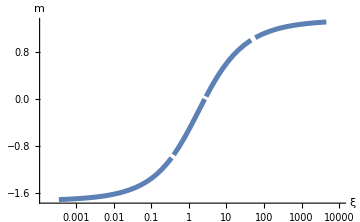
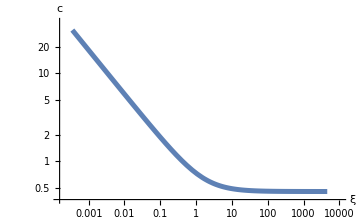
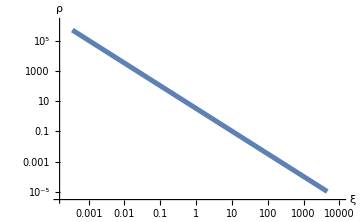

```mathematica
plot profiles supersonic[γval_,ηval_,ξsval_]:=Module[{ξ sonic eqn, ξsi,ξso,mder,
ξ inner low,ξ inner high,ξ outer low,ξ outer high,
m inner low,m outer high,
ξ asymptotic low,ξ asymptotic high, m asymptotic high,m asymptotic low,
ξ freefall low,ξ freefall high,m freefall high,
sol inner,sol outer, sol asymptotic, sol freefall,universol},
ξ sonic eqn= mach number derivative/.{γ->γval,η->ηval,ξs->ξsval};
ξ sonic eqn = Simplify[ξ sonic eqn];
ξ sonic eqn = Numerator[ξ sonic eqn];
ξ sonic eqn = ξ sonic eqn/.m->1;
ξ sonic eqn = Simplify[ξ sonic eqn];
ξ sonic eqn = Simplify[ξ sonic eqn/ξ^Limit[ξ D[Log[ξ sonic eqn], ξ],ξ->0]];
ξsi = ξ/.FindRoot[ξ sonic eqn==0,{ξ,0,ξsval*0.99}][[1]];
ξso = ξ/.FindRoot[ξ sonic eqn==0,{ξ,ξsval*1.1,10^6*ξsval}];
ξ freefall low=ξsi/10^3;
ξ freefall high=ξsi*(1-10^-6);
ξ inner low = ξsi*(1+10^-6);
ξ inner high = ξsval*(1-10^-6);
ξ outer low = ξsval*(1+10^-6);
ξ outer high=ξso*(1-10^-6);
ξ asymptotic low = ξso*(1+10^-6);
ξ asymptotic high=100*ξso;
m freefall high=-1*(ξ freefall high-ξsval)/(ξsi-ξsval);
m inner low=-1*(ξ inner low-ξsval)/(ξsi-ξsval);
m outer high=1*(ξ outer high-ξsval)/(ξso-ξsval);
m asymptotic low = 1*(ξ asymptotic low-ξsval)/(ξso-ξsval);
m asymptotic high=Chop[(asymptotic mach number/.{γ->γval,η->ηval})];
mder = mach number derivative;
mder = mder/.{γ->γval,η->ηval,ξs->ξsval,m->m[ξ]};
sol freefall = m[ξ]/.NDSolve[{m'[ξ]==mder,m[ξ freefall high]==m freefall high},m[ξ],{ξ,ξ freefall low,ξ freefall high}][[1]];
sol inner = m[ξ]/.NDSolve[{m'[ξ]==mder,m[ξ inner low]==m inner low},m[ξ],{ξ,ξ inner low,ξ inner high}][[1]];
sol outer = m[ξ]/.NDSolve[{m'[ξ]==mder,m[ξ outer high]==m outer high},m[ξ],{ξ,ξ outer low,ξ outer high}][[1]];
sol asymptotic = m[ξ]/.NDSolve[{m'[ξ]==mder,m[ξ asymptotic low]==m asymptotic low},m[ξ],
{ξ,ξ asymptotic low,ξ asymptotic high}][[1]];
universol=Piecewise[{
{sol asymptotic,ξ>ξso},
{sol outer,ξso>ξ>ξsval},
{sol inner,ξsval>ξ>ξsi},
{sol freefall,ξsi>ξ}}];
{
LogLinearPlot[universol,
{ξ,ξ freefall low,ξ asymptotic high},
AxesLabel->{ξ,m},
PlotStyle->Thickness[0.01],
BaseStyle->{FontWeight->"Bold",FontSize->18},
ImageSize->Medium
],
LogLogPlot[dimles c/.{m-> universol,γ->γval,η->ηval,ξs->ξsval},
{ξ,ξ freefall low,ξ asymptotic high},
AxesLabel->{ξ,c},
PlotStyle->Thickness[0.01],
BaseStyle->{FontWeight->"Bold",FontSize->18},
ImageSize->Medium],
LogLogPlot[dimles ρ/.{m-> universol,γ->γval,η->ηval,ξs->ξsval},
{ξ,ξ freefall low,ξ asymptotic high},
AxesLabel->{ξ,ρ},
PlotStyle->Thickness[0.01],
BaseStyle->{FontWeight->"Bold",FontSize->18},
ImageSize->Medium]
}
]
plot profiles supersonic[5./3.,2.5,8/3]
```

```mathematica
ξs/.FindRoot[shoot outside in[4./3.,2.5,ξs],{ξs,2,20},Evaluated->False]
```

4.72104

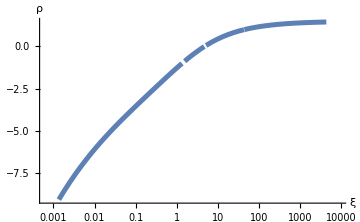
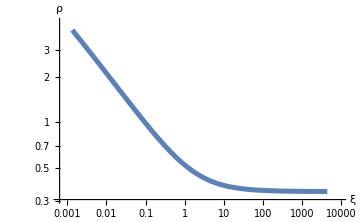
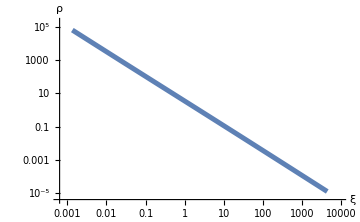

```mathematica
plot profiles supersonic[4./3.,2.5,4.721]
```

```mathematica
ξs/.FindRoot[shoot outside in[4./3.,2.9,ξs],{ξs,2,20},Evaluated->False]
```

4.07642

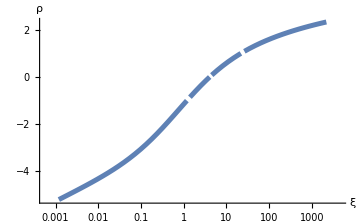
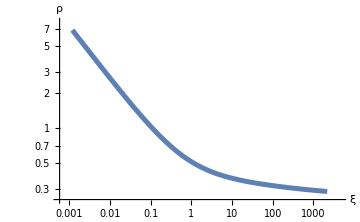
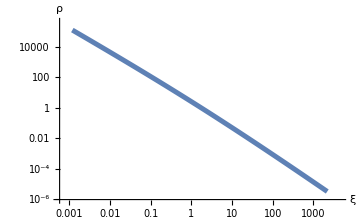

```mathematica
plot profiles supersonic[4./3.,2.9,4.08]
```

```mathematica
ξs/.FindRoot[shoot outside in[5./3.,2.3,ξs],{ξs,2,20},Evaluated->False]
```

2.88539

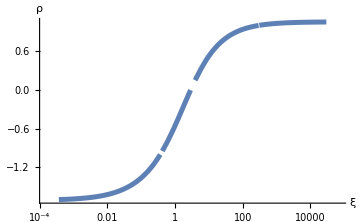
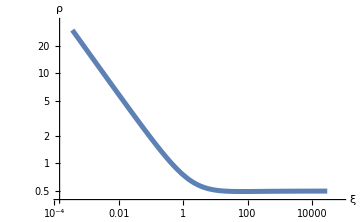
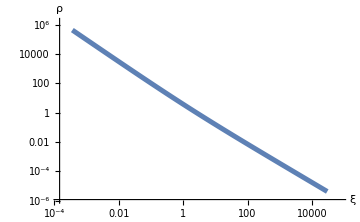

```mathematica
plot profiles supersonic[5./3.,2.3,2.885]
```

Subsonic case

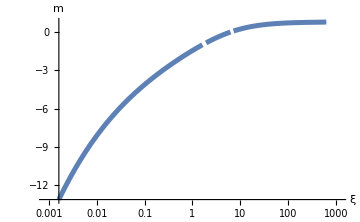
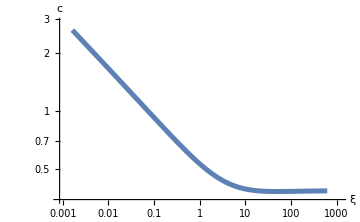
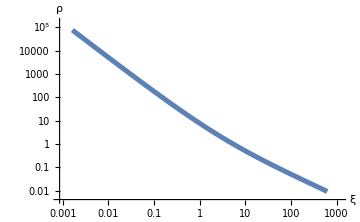

```mathematica
plot profiles subsonic[γval_,ηval_,ξsval_]:=Module[{ξ sonic eqn, ξsi,mder,
ξ inner low,ξ inner high,ξ outer low,ξ outer high,
m inner low,m outer high,
ξ asymptotic low,ξ asymptotic high, m asymptotic high,m asymptotic low,
ξ freefall low,ξ freefall high,m freefall high,
sol inner,sol outer, sol asymptotic, sol freefall,universol},
ξ sonic eqn= mach number derivative/.{γ->γval,η->ηval,ξs->ξsval};
ξ sonic eqn = Simplify[ξ sonic eqn];
ξ sonic eqn = Numerator[ξ sonic eqn];
ξ sonic eqn = ξ sonic eqn/.m->1;
ξ sonic eqn = Simplify[ξ sonic eqn];
ξ sonic eqn = Simplify[ξ sonic eqn/ξ^Limit[ξ D[Log[ξ sonic eqn], ξ],ξ->0]];
ξsi = ξ/.FindRoot[ξ sonic eqn==0,{ξ,0,ξsval*0.99}][[1]];
ξ freefall low=ξsi/10^3;
ξ freefall high=ξsi*(1-10^-6);
ξ inner low = ξsi*(1+10^-6);
ξ inner high = ξsval*(1-10^-6);
ξ asymptotic low=ξsval*(1+10^-6);
ξ asymptotic high=100*ξsval;
m freefall high=-1*(ξ freefall high-ξsval)/(ξsi-ξsval);
m inner low=-1*(ξ inner low-ξsval)/(ξsi-ξsval);
m asymptotic high=Chop[(asymptotic mach number/.{γ->γval,η->ηval})];
mder = mach number derivative;
mder = mder/.{γ->γval,η->ηval,ξs->ξsval,m->m[ξ]};
sol freefall = m[ξ]/.NDSolve[{m'[ξ]==mder,m[ξ freefall high]==m freefall high},m[ξ],{ξ,ξ freefall low,ξ freefall high}][[1]];
sol inner = m[ξ]/.NDSolve[{m'[ξ]==mder,m[ξ inner low]==m inner low},m[ξ],{ξ,ξ inner low,ξ inner high}][[1]];
sol asymptotic = m[ξ]/.NDSolve[{m'[ξ]==mder,m[ξ asymptotic high]==m asymptotic high},m[ξ],
{ξ,ξ asymptotic low,ξ asymptotic high}][[1]];
universol=Piecewise[{
{sol asymptotic,ξ>ξsval},
{sol inner,ξsval>ξ>ξsi},
{sol freefall,ξsi>ξ}}];
{
LogLinearPlot[universol,
{ξ,ξ freefall low,ξ asymptotic high},
AxesLabel->{ξ,m},
LabelStyle-> Directive[Bold],
AxesOrigin-> {ξ freefall low,universol/.ξ->ξ freefall low},
BaseStyle->{FontWeight->"Bold",FontSize->18},
PlotStyle->Thickness[0.01],
ImageSize->Medium
],
LogLogPlot[Abs[dimles c]/.{m-> universol,γ->γval,η->ηval,ξs->ξsval},
{ξ,ξ freefall low,ξ asymptotic high},
AxesLabel->{ξ,c},
PlotRange->Full,
PlotStyle->Thickness[0.01],
BaseStyle->{FontWeight->"Bold",FontSize->18},
ImageSize->Medium
],
LogLogPlot[Abs[dimles ρ]/.{m-> universol,γ->γval,η->ηval,ξs->ξsval},
{ξ,ξ freefall low,ξ asymptotic high},
AxesLabel->{ξ,ρ},
PlotStyle->Thickness[0.01],
BaseStyle->{FontWeight->"Bold",FontSize->18},
ImageSize->Medium
]
}
]
plot profiles subsonic[4./3.,1.9,6.26]
```